# Modelagem Idempotente para Cabos SC Ajuste das funções via VF

O objetivo desse notebook é apresentar o cálculo dos idempotentes e tentar realizar o ajuste via VF ou OVF

## Início

```mathematica
Clear["Global`*"]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Documents and Settings\Administrador\Escritorio

```mathematica
<<LCParam`
```

## Opções de programa

```mathematica
SetOptions[{ListPlot,ListLogPlot,ListLogLinearPlot,ListLogLogPlot},Axes->False,Frame->True,PlotRange->All,Joined->True,ImageSize->350,PlotStyle->{PointSize[0.015]},BaseStyle->{14,FontFamily->"Helvetica"}];
```

```mathematica
plstyle1={AbsoluteThickness[2],RGBColor[1,0,0]};
plstyle2={AbsoluteThickness[2],RGBColor[0,0,1]};
plstyle3={AbsoluteThickness[2],PointSize[.015],RGBColor[0,1,0]};
```

## Configuração da Rede

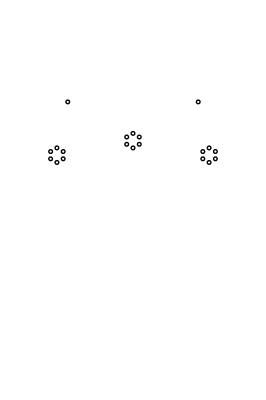

```mathematica
xc={-10.5,-9.63397459621556,-9.63397459621556,-10.5,-11.36602540378444,-11.36602540378444,0.,0.8660254037844386,0.8660254037844386,0.,-0.8660254037844386,-0.8660254037844386,10.5,11.36602540378444,11.36602540378444,10.5,9.63397459621556,9.63397459621556,-9.,9.};
 yc={27.669999999999998,28.169999999999998,29.169999999999998,29.669999999999998,29.169999999999998,28.169999999999998,29.67,30.17,31.17,31.67,31.17,30.17,27.669999999999998,28.169999999999998,29.169999999999998,29.669999999999998,29.169999999999998,28.169999999999998,36.00333333333333,36.00333333333333};
mostra=Table[{Circle[{xc[[i]],yc[[i]]},0.25]},{i,1,Length[xc]}];
tsimples=Show[Graphics[mostra],AspectRatio->Automatic,Axes->False,Frame->Automatic,PlotRange->{{-15,15},{0,45}},FrameLabel->{"distância (m)","distância (m)"}]
```

## Dados de Entrada

```mathematica
ncond=Length[xc];
nfeixe=6;
nfases=3;
npr=2;
```

```mathematica
(* rf=.908 *10^-2; *)
rf=29.591*10^-3/2;
rint=7.3914*10^-3/2; 
rpr=4.57*10^-3;
```

```mathematica
ϵ=8.854 10^-12;
```

```mathematica
ρc=0.06114292531162*10^-3 * π* rf^2;
ρpr=4.19*10^-3* π  *rpr^2;
```

```mathematica
ρsolo= 100;
(*tempfase=60;
fencalum=0.750223;
αtemp=0.00454562;
σc=fencalum/(ρ00(1+αtemp tempfase));
ρc=1/σc;*)
```

```mathematica
compr=1000;
```

```mathematica
sigma=1/ρsolo;
(*kprima[sigma_,Omega_]:=(sigma)+(10^-6)*(0.057849+I*0.12097)*(Omega^0.71603);*)
kprima[sigma_,Omega_]:=(sigma);
G1=DiagonalMatrix[Table[10^-12,{nfases}]];
```

## Frequências e Inicialização das Listas

### Freqüências de interesse

#### Faixa de Frequência

```mathematica
d1=-1;
d2=N[7.,40];
n=100;
freqlog[i_,f_,np_]:=Table[N[10^(i+x(f-i)/(Floor[np]-1))],{x,0,np-1}]
freqlin[i_,f_,np_]:=Table[N[(i+x(f-i)/(Floor[np]-1))],{x,0,np-1}]
(*f0=freqlog[d0,d1,500];*)
f1=freqlog[d1,d2,n];
f2=freqlin[10^d1, 10^d2,n];
f=Sort@Union[f2,f1];
nf=Length[f];
```

```mathematica
sk=2*π*f;
nf=Length[sk]
```

198

### Inicialização das listas

```mathematica
T=T1=λ0=Γ1=Yc1=Af1=Am1=Am2=M1=M2=γm=Table[0,{n,1,nf}];
```

## Rotinas Auxiliares

### ROT

```mathematica
rot[s_?MatrixQ]:=Module[{S=s,Nc,SA,SB,scale,ang,scale1,col,scale2,err1,err2,numerator,denominator,aaa,bbb,ccc},
Nc=Length[S];
SA=Table[0,{Nc},{Nc}];
SB=SA;
scale1=Table[0,{Nc}];
scale2=scale=ang=scale1;
err1=scale1;
err2=scale1;

numerator=Table[0,{Nc}];
denominator=numerator=scale1=scale2;

For[col=1,col≤ Nc,col++,
numerator[[col]]=0.;
denominator[[col]]=numerator[[col]]=0.;

For[j=1,j≤ Nc,j++,
numerator[[col]]=numerator[[col]]+Im[S[[j,col]]]*Re[S[[j,col]]];
denominator[[col]]=denominator[[col]]+Re[S[[j,col]]]^2-Im[S[[j,col]]]^2];

numerator[[col]]=-2*numerator[[col]];
ang[[col]]=0.5*ArcTan[denominator[[col]],numerator[[col]]];
scale1[[col]]=Cos[ang[[col]]]+ⅈ*Sin[ang[[col]]];
scale2[[col]]=Cos[ang[[col]]+π/2.]+ⅈ*Sin[ang[[col]]+π/2.];

For[j=1,j≤ Nc,j++,
SA[[j,col]]=S[[j,col]]*scale1[[col]];
SB[[j,col]]=S[[j,col]]*scale2[[col]];];

aaa=0.;
bbb=0.;
ccc=0.;

For[j=1,j≤ Nc,j++,
aaa=aaa+Im[SA[[j,col]]]^2;
bbb=bbb+Re[SA[[j,col]]]*Im[SA[[j,col]]];
ccc=ccc+Re[SA[[j,col]]]^2];

err1[[col]]=aaa*Cos[ang[[col]]]^2+bbb*Sin[N[2*ang[[col]],16]]+ccc*Sin[ang[[col]]]^2;

aaa=0.;
bbb=0.;
ccc=0.;

For[j=1,j≤ Nc,j++,
aaa=aaa+Im[SB[[j,col]]]^2;
bbb=bbb+Re[SB[[j,col]]]*Im[SB[[j,col]]];
ccc=ccc+Re[SB[[j,col]]]^2];

err2[[col]]=aaa*Cos[ang[[col]]]^2+bbb*Sin[N[2*ang[[col]],16]]+ccc*Sin[ang[[col]]]^2;

If[err1[[col]]<err2[[col]],scale[[col]]=scale1[[col]],scale[[col]]=scale2[[col]]];

S[[All,col]]=S[[All,col]]*scale[[col]];
];
Return[S]
]
```

### Elimina o Cruzamento de Autovetores (Newton-Raphson)

```mathematica
eigNR[G_?MatrixQ,V0_,d0_,Tol_:10^-10]:=Module[{A=G,nc,scale,v,d,vec,res,jac,i},
nc=Length[A];
scale=Norm[A];
A=A/scale;
outd=Table[0,{nc}];
outv=Table[0,{nc},{nc}];
itr=0;
jac=Table[0.0,{nc+1},{nc+1}];
Do[{v=V0[[1;;,i]];
d=d0[[i]];
res=Max[Abs[A.v-v*d]];
While[(res>Tol)&& (itr<10000),
itr=itr+1;
jac[[1;;nc,1;;nc]]=A-d*IdentityMatrix[nc];
jac[[1;;nc,nc+1]]=-v;
jac[[nc+1,1;;nc]]=2*v;
res=Join[A.v-v*d,{v.v-1}];
vec=LinearSolve[jac,res];
res=Max[Abs[vec]];
v=v-vec[[1;;nc]];
d=d-vec[[nc+1]];
];
outd[[i]]=d*scale;
outv[[1;;,i]]=Normalize[v];},{i,1,nc}]];
```

### Decompor Matriz (n x n) em elementos

```mathematica
descompmatrlargaAsimetrica[Matr_]:=Module[{kk,nm,Matr2},
Matr2=Table[0,{N[Max[Dimensions[Matr]]]},{N[Min[Dimensions[Matr]]]*(N[Min[Dimensions[Matr]]])}];
For[nm=1,nm≤N[Max[Dimensions[Matr]]],nm++,
kk=0;
Table[kk++;Matr2[[nm,kk]]=Matr[[nm,i,j]],{i,1,N[Min[Dimensions[Matr]]]},{j,1,N[Min[Dimensions[Matr]]]}]];
Return[Matr2]]
```

### UnwrapPhase

```mathematica
(***********UnwrapPhase follows*************)UnwrapPhase[data_?VectorQ,tol_:Pi,inc_:2 Pi]:=FixedPoint[#+inc*FoldList[Plus,0.,Sign[Chop[ListCorrelate[{1,-1},#],tol]   (*close Chop*)]    (*close Sign*)]&,(*close FoldList*)data]   (*close FixedPoint and overall function*)

UnwrapPhase[list:{{_,_}..}]:=Transpose[{list[[All,1]],UnwrapPhase[list[[All,-1]]]}]
(***********UnwrapPhase above*************)
```

## Principal Loop de Frequência

```mathematica
YNodal=ytraco=gamma=Evals=T2=HTr=Ycm1=Yc1=Table[0,{nf}];
```

```mathematica
AbsoluteTiming[Do[{ω=sk[[nm]],
MontaMatrizes[ncond,npr,nfeixe,kprima[sigma,ω],ρc,ρpr,rf,rint,rpr,xc,yc,ω],
Yc=Inverse[Inverse[Y1].MatrixPower[Y1.Z1,0.5]],

Yn=Ynodal[Z1,Y1,compr];
ytraco[[nm]]=Tr[Yn],

Γ= N[Y1.Z1,40],
gamma[[nm]]=Γ;
k=nm,

If[nm==1,
{eval,evec}=Eigensystem[Γ];
 evelho=rot[Transpose[evec]],
eigNR[Γ,evelho,eval];
eval=outd;
evelho=outv;
],

If[nm==1,
{eval2,evec2}=Eigensystem[Yc];
 evelho2=rot[Transpose[evec2]],
eigNR[Yc,evelho2,eval2];
eval2=outd;
evelho2=outv;
] ,

λ0[[nm]]=Sqrt[eval];
α1=Exp[-λ0[[nm]] compr];
Am1[[nm]]=α1;
T[[nm]]=evelho,
Evals[[nm]]=eval,

Afase=evelho.DiagonalMatrix[Am1[[nm]]].Inverse[evelho]; (*corregido*)
Af1[[nm]]=Select[Flatten[UpperTriangularize[Afase]],Abs[#1]>0&];
(*Afase2[[nm]]=MatrixExp[-MatrixPower[Γ,0.5] compr]*)
HTr[[nm]]=Tr[Afase];

Ycm1[[nm]]=eval2;
Yc1[[nm]]=Select[Flatten[UpperTriangularize[Yc]],Abs[#1]>0&]

},{nm,1,nf}]]
```

{9.078125,Null}

```mathematica
nc=Length[Afase]
```

3

# Implementação do RVF

## Dados de Entrada

### Polos Iniciais

```mathematica
omega=sk;
```

```mathematica
fmax=Last@omega;
fmin=First@omega;
npolini=15;
```

```mathematica
polini=Flatten[Table[{-(ff)/100+ⅈ*(ff),-(ff)/100-ⅈ*(ff)},{ff,fmin,fmax,(fmax-fmin)/((npolini-1)/2)}]];
```

# Vector Fitting

### Funções Auxiliares

```mathematica
idx[polos_List]:=Module[{np,fun,ind},
np=Length[polos];
ind=0*Range[1,np];
fun=Map[Head,polos];
Do[If[fun[[mm]]==Complex,
If[mm==1,ind[[mm]]=1,
If[ind[[mm-1]]==0 ∨ ind[[mm-1]]==2 ,ind[[mm]]=1;ind[[mm+1]]=2,
ind[[mm]]=2]]],{mm,1,np}];
Return[ind]];

Aux[s_,p_List,index_List]:=With[
{np=Length[p]},
Table[If[index[[mm]]==0.,
(1/(s-p[[mm]])),If[index[[mm]]==1.,
(1/(s-p[[mm]])+1/(s-p[[mm+1]])),
(ⅈ/(s-p[[mm-1]])-ⅈ/(s-p[[mm]]))]],
{mm,np}]];

Aux2[s_,p_List,index_List]:=With[
{np=Length[p]},
Table[If[index[[mm]]==0.,
(Sqrt[2*Abs[p[[mm]]]])/(s-p[[mm]])*Product[(s+Conjugate[p[[kk]]])/(s-p[[kk]]),
{kk,1,mm-1}],
If[index[[mm]]==1.,
(Sqrt[-2*Re[p[[mm]]]])*(s-Abs[p[[mm]]])/((s-p[[mm]])*(s-p[[mm+1]]))*Product[(s+Conjugate[p[[kk]]])/(s-p[[kk]]),
{kk,1,mm-1}],
(Sqrt[-2*Re[p[[mm]]]])*(s+Abs[p[[mm]]])/((s-p[[mm-1]])*(s-p[[mm]]))*Product[(s+Conjugate[p[[kk]]])/(s-p[[kk]]),
{kk,1,mm-2}]]],
{mm,np}]];
```

# Cálculos dos Pólos com o RVF

```mathematica
RVFpolos[polos_List,freq_List,data_,termoD_:1,termoE_:1]:=Module[{npol,nfreq,ss,indices,Anum,UmS,Anum2,Af,AA,BB,XX,Csigma,Azeros,Bzeros,Czeros,Dzeros,polaux,polosN,weight,Ws,RVF,i,j,q,r,AAA,BBB,AAAT,normas,Xaux,AAAaux,AAAscale,scale},
npol=Length[polos];
nfreq=Length[freq];
ss=ⅈ*N[freq];

indices=idx[polos];
Anum=Transpose[Aux[ss[[Range[nfreq]]],polos,indices]];

UmS=If[termoD==1∧termoE==1,{1,ss[[#]]}&/@Range[nfreq],
If[termoD==1∧termoE==0,{1}&/@Range[nfreq],
If[termoD==0∧termoE==1,{ss[[#]]}&/@Range[nfreq],{}&/@Range[nfreq]]]];
Anum2=-data*Anum;

weight=Table[1,{nfreq}];
Ws=Norm[Table[weight[[i]]*data[[i]],{i,1,nfreq}]]/nfreq;

RVF=Flatten[{Table[0,{npol+termoD+termoE}],Table[Sum[Re[Anum[[i,j]]],{i,1,nfreq}],{j,1,npol}],nfreq}]*Ws;
Af=Flatten[{Anum[[#]],UmS[[#]],Anum2[[#]],-data[[#]]}*weight[[#]]]&/@Range[nfreq];
AA=Join[Re[Af],Im[Af],{RVF}];
BB=Flatten[{0*Range[1,2*nfreq],nfreq}]*Ws;

AAA=Take[QRDecomposition[AA][[2]],-npol-1,-npol-1];
BBB=Take[QRDecomposition[AA][[1]],-npol-1].BB;

AAAT=Transpose[AAA];
normas=Norm[AAAT[[#]]]&/@Range[1,npol+1];
AAAaux=AAAT/normas;

AAAscale=Transpose[AAAaux];
Xaux=LeastSquares[AAAscale,BBB];
scale=1/normas;
XX=Xaux*scale;

Azeros=Table[0,{npol},{npol}];
Bzeros=Table[{0},{npol}];
Bzeros=Table[If[indices[[mm]]==0,Bzeros[[mm]]={1},If[indices[[mm]]==1,Bzeros[[mm]]={2},{0}]],{mm,npol}];
Czeros=Partition[XX[[Range[1,npol]]],1];
Dzeros=XX[[-1]];

Do[If[indices[[mm]]== 0,Azeros[[mm,mm]]=polos[[mm]],If[indices[[mm]]== 1,Azeros[[mm,mm]]=Re[polos[[mm]]];Azeros[[mm,mm+1]]=Im[polos[[mm]]];Azeros[[mm+1,mm]]=-Im[polos[[mm]]];Azeros[[mm+1,mm+1]]=Re[polos[[mm]]]],0],{mm,npol}];

polaux=Eigenvalues[Azeros-(Bzeros/Dzeros).Transpose[Czeros]];
polosN=-Abs[Re[polaux]]+ⅈ Im[polaux];

Return[polosN]]
```

# Cálculo dos Resíduos

### Cálculo dos Resíduos

```mathematica
res[polos_List,freq_List,data_List,termoD_:1.,termoE_:1.]:=Module[{npol,nfreq,ss,indices,AAnum,UUmS,AAf,AAff,AAffT,normas,BBff,XXff,resfim,dd,ee,naux,AAAaux,AAAscale,Xaux,scale},

npol=Length[polos];
nfreq=Length[freq];
ss=ⅈ*N[freq];

indices=idx[polos];

AAnum=Transpose[Aux[ss[[Range[nfreq]]],polos,indices]];

UUmS=If[termoD==1∧termoE==1,{1,ss[[#]]}&/@Range[nfreq],
If[termoD==1∧termoE==0,{1}&/@Range[nfreq],
If[termoD==0∧termoE==1,{ss[[#]]}&/@Range[nfreq],{}&/@Range[nfreq]]]];

AAf=Flatten[{AAnum[[#]],UUmS[[#]]}]&/@Range[nfreq];

AAff=ArrayFlatten[{{Re[AAf]},{Im[AAf]}}];
BBff=Flatten[{Re[data],Im[data]}];

naux=termoD+termoE;

AAffT=Transpose[AAff];
normas=Norm[AAffT[[#]]]&/@Range[1,npol+naux];
AAAaux=AAffT/normas;

AAAscale=Transpose[AAAaux];
Xaux=LeastSquares[AAAscale,BBff];
scale=1/normas;
XXff=Xaux*scale;

resfim=0*Range[1,npol];

Do[If[indices[[nm]]==0,resfim[[nm]]=XXff[[nm]],If[indices[[nm]]==1,resfim[[nm]]=XXff[[nm]]+ⅈ*XXff[[nm+1]];resfim[[nm+1]]=XXff[[nm]]-ⅈ*XXff[[nm+1]],0]],{nm,npol}];

If[termoD==1∧termoE==1,dd=XXff[[-2]];ee=XXff[[-1]],
If[termoD==1∧termoE==0,dd=XXff[[-1]];ee=0,
If[termoD==0∧termoE==1,dd=0;ee=XXff[[-1]],dd=0;ee=0]]];

Return[{resfim,dd,ee}]]
```

# Outros Calculos

```mathematica
calcelem[polos_List,residuos_List,omega_List,yElementos_,TermD_,TermE_,nres_]:=Module[{funcoes,Pontos,dif,RMSD},
funcoes=Table[Sum[(residuos[[i,kk]]/(s-polos[[kk]])),{kk,Length[polos]}]+TermD[[i]]+s*TermE[[i]],{i,nres}];
Pontos=Transpose[Table[Map[(funcoes[[i]]/.s->#)&,ⅈ omega],{i,nres}]];
dif=Sqrt[Abs[(Pontos-yElementos)^2]/Length[omega]];
RMSD=Sqrt[Total[Abs[Pontos-yElementos]^2]/Length[omega]];
Return[{funcoes,Pontos,RMSD,dif}]]
```

```mathematica
calctraco[polos_List,residuos_List,omega_,data_,termoD_,termoE_]:=Module[{funcoes,Pontos,difRMS,dif},
funcoes=Table[Sum[(residuos[[kk]]/(s-polos[[kk]])),{kk,Length[polos]}]+termoD+s*termoE];
Pontos=Map[(funcoes/.s->#)&,ⅈ omega];
difRMS=Sqrt[Total[Abs[(Pontos-data)^2]]]/Sqrt[Length[omega]];
dif=Sqrt[Abs[(Pontos-data)^2]]/Sqrt[Length[omega]];
Return[{funcoes,Pontos,difRMS,dif}]]
```

```mathematica
descompmatr[Matr_]:=Module[{A=Matr},Select[Flatten[UpperTriangularize[A]],Abs[#]>0&]];
```

```mathematica
recompmatr[Matr_]:=Module[{A=Matr,ncond2,k,Mrecomp},
ncond2=Floor[0.5(-1+Sqrt[1+8*Length[A]])];
Mrecomp=Table[0,{ncond2},{ncond2}];
For[k=1,k<ncond2+1,k++,Mrecomp[[ncond2-k+1,ncond2-k+1;;ncond2]]=Take[A,-k];A=Take[A,Length[A]-k]];
Table[Mrecomp[[j,i]]=Mrecomp[[i,j]],{i,1,ncond2},{j,1,ncond2}];
Return[Mrecomp]]
```

```mathematica
recompmatrlarga[Matr_]:=Module[{A=Matr,Matr2},
Matr2=Table[0,{N[Max[Dimensions[A]]]}];
Table[Matr2[[j]]=recompmatr[A[[j]]],{j,1,N[Max[Dimensions[A]]]}];
Return[Matr2]]
```

```mathematica
descompmatrlarga[Matr_]:=Module[{A=Matr,Matr2},
Matr2=Table[0,{N[Max[Dimensions[A]]]}];
Table[Matr2[[j]]=descompmatr[A[[j]]],{j,1,N[Max[Dimensions[A]]]}];
Return[Matr2]]
```

# Ajuste de H x Exp[I ω τ]

```mathematica
tmin=compr/(3*10^8);
tmax=1.0025*tmin;
num=200;
```

```mathematica
tau=Table[(tmin+i (tmax-tmin)/num),{i,1,num}];
```

```mathematica
erroRMS=Table[0,{num},{Min[Dimensions[Am1]]}];
```

```mathematica
TemD=0.;
TemE=0.;
ppolos=N[polini];
niter=N[25];
```

```mathematica
Dimensions[Am1]
```

{198,3}

```mathematica
AbsoluteTiming[Do[Module[{polosRVF,residuosRVF,TermDRVF,TermERVF,PontosRVFElem,difRMSRVF,difRVF},
yElementos=Am1[[#]] Exp[I omega[[#]] tau[[mm]]]&/@Range[1,nf];
ytraco=Tr[yElementos[[#]]]&/@Range[nf];

AbsoluteTiming[Do[pp=RVFpolos[ppolos,omega,ytraco,TemD,TemE];ppolos=pp,{niter}]];
polosRVF=ppolos;
residuosRVF=TermDRVF=TermERVF=ConstantArray[0,nc];

Do[{residuosRVF[[nm]],TermDRVF[[nm]],TermERVF[[nm]]}=res[polosRVF,omega,yElementos[[All,nm]],TemD,TemE],{nm,nc}];
{funcoesRVF,PontosRVFElem,difRMSRVF,difRVF}=calcelem[polosRVF,residuosRVF,omega,yElementos,TermDRVF,TermERVF,nc];

erroRMS[[mm]]=difRMSRVF],{mm,num}]]
```

{296.71875,Null}

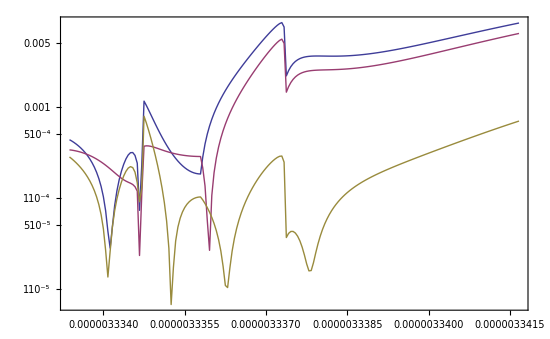

```mathematica
ListLogPlot[Transpose@{tau,erroRMS[[All,#]]}&/@Range[1,nc],PlotStyle->Thick,ImageSize->550]
```

```mathematica
aux=Flatten[Position[erroRMS,Min[erroRMS[[All,#]]]]]&/@Range[nc];
pos=aux[[#,1]]&/@Range[nc]
```

{19,32,46}

```mathematica
tauvector=tau[[pos[[#]]]]&/@Range[nc]
```

{3.33413×10^-6,3.33467×10^-6,3.33525×10^-6}

# Ajuste de Elementos de Yc modal

```mathematica
Ycm1Tr=Tr[Ycm1[[#]]]&/@Range[nf];
```

```mathematica
TemD=1.;
TemE=0.;
npolini=10;
polini=Flatten[Table[{-(ff)/100+ⅈ*(ff),-(ff)/100-ⅈ*(ff)},{ff,fmin,fmax,(fmax-fmin)/((npolini-1)/2)}]];
ppolos=N[polini];
niter=N[15];
```

```mathematica
AbsoluteTiming[Do[pp=RVFpolos[ppolos,omega,Ycm1Tr,TemD,TemE];ppolos=pp,{niter}]];
polosRVFYc1=ppolos;
```

```mathematica
residuosRVFYcm1=TermDRVFYcm1=TermERVFYcm1=ConstantArray[0,nc];Do[{residuosRVFYcm1[[nm]],TermDRVFYcm1[[nm]],TermERVFYcm1[[nm]]}=res[polosRVFYc1,omega,Ycm1[[All,nm]],TemD,TemE],{nm,nc}];
{funcoesRVF,PontosRVFElemYcm1,difRMSRVFYcm1,difRVFYcm1}=calcelem[polosRVFYc1,residuosRVFYcm1,omega,Ycm1,TermDRVFYcm1,TermERVFYcm1,nc];
```

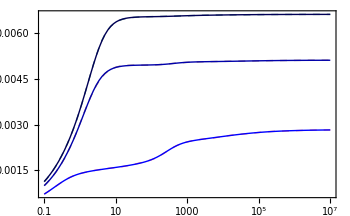
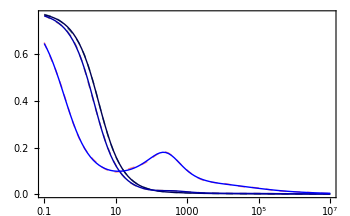

```mathematica
GrelemRVF=ListLogLinearPlot[Map[Transpose@{omega/(2 Pi),Abs[PontosRVFElemYcm1[[All,#]]]}&,Range[nc]],PlotStyle->Table[{Thick,RGBColor[i/nc,0.5,0.5],Dashed},{i,nc}]];
GrElemfun=ListLogLinearPlot[Map[Transpose@{omega/(2 Pi),Abs[Ycm1[[All,#]]]}&,Range[nc]],PlotStyle->Table[{Thin,RGBColor[0,0,i/nc]},{i,nc}]];

GrelemRVFArg=ListLogLinearPlot[Map[Transpose@{omega/(2 Pi),Arg[PontosRVFElemYcm1[[All,#]]]}&,Range[nc]],PlotStyle->Table[{Thick,RGBColor[i/nc,0.5,0.5],Dashed},{i,nc}]];
GrElemfunArg=ListLogLinearPlot[Map[Transpose@{omega/(2 Pi),Arg[Ycm1[[All,#]]]}&,Range[nc]],PlotStyle->Table[{Thin,RGBColor[0,0,i/nc]},{i,nc}]];

{Show[{GrelemRVF,GrElemfun}],Show[{GrelemRVFArg,GrElemfunArg}]}
```

## Error del Ajuste de Yc modal

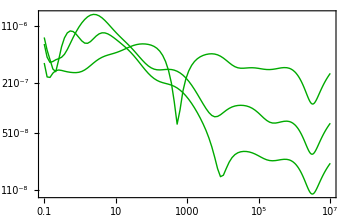

```mathematica
ErroRVFf=ListLogLogPlot[Map[Transpose@{omega/(2 Pi),difRVFYcm1[[All,#]]}&,Range[nc]],PlotStyle->Darker[Green]]
```

# Ajuste de H modal

## Multiplicacao da Funcao de Propagacao pelo Exp[I ω τ] (τ = Vetor Time Delay)

```mathematica
Am2=Am1[[#]] Exp[I omega[[#]] tauvector]&/@Range[1,nf];
Am2Tr=Tr[Am2[[#]]]&/@Range[nf];
```

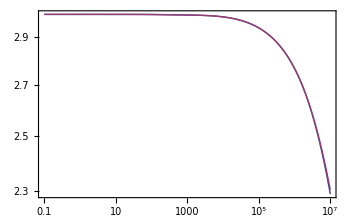
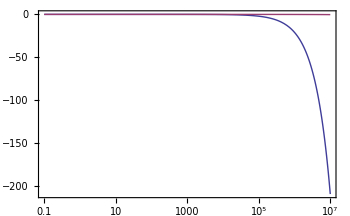

```mathematica
Gr1=ListLogLogPlot[{Transpose@{omega/(2 Pi),Abs[HTr]},Transpose@{omega/(2 Pi),Abs[Am2Tr]}}];
Gr2=ListLogLinearPlot[{Transpose@{omega/(2 Pi),UnwrapPhase[Arg[HTr]]},Transpose@{omega/(2 Pi),UnwrapPhase[Arg[Am2Tr]]}}];
{Gr1,Gr2}
```

## Ajuste de elementos de H modal

```mathematica
TemD=0.;
TemE=0.;
npolini=12;
polini=Flatten[Table[{-(ff)/100+ⅈ*(ff),-(ff)/100-ⅈ*(ff)},{ff,fmin,fmax,(fmax-fmin)/((npolini-1)/2)}]];
ppolos=N[polini];
niter=N[10];
```

```mathematica
AbsoluteTiming[Do[pp=RVFpolos[ppolos,omega,Am2Tr,TemD,TemE];ppolos=pp,{niter}]];
polosRVFAm2=ppolos;
```

```mathematica
residuosRVFAm2=TermDRVFAm2=TermERVFAm2=ConstantArray[0,nc];Do[{residuosRVFAm2[[nm]],TermDRVFAm2[[nm]],TermERVFAm2[[nm]]}=res[polosRVFAm2,omega,Am2[[All,nm]],TemD,TemE],{nm,nc}];
{funcoesRVF,PontosRVFElemAm2,difRMSRVFAm2,difRVFAm2}=calcelem[polosRVFAm2,residuosRVFAm2,omega,Am2,TermDRVFAm2,TermERVFAm2,nc];
```

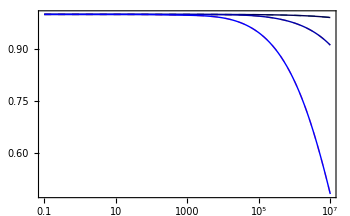
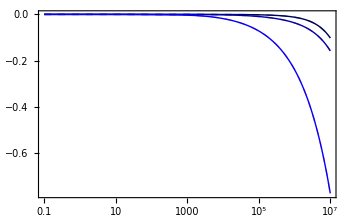

```mathematica
GrelemRVF=ListLogLinearPlot[Map[Transpose@{omega/(2 Pi),Abs[PontosRVFElemAm2[[All,#]]]}&,Range[nc]],PlotStyle->Table[{Thick,RGBColor[i/nc,0.5,0.5],Dashed},{i,nc}]];
GrElemfun=ListLogLinearPlot[Map[Transpose@{omega/(2 Pi),Abs[Am2[[All,#]]]}&,Range[nc]],PlotStyle->Blue];

GrelemRVFArg=ListLogLinearPlot[Map[Transpose@{omega/(2 Pi),Arg[PontosRVFElemAm2[[All,#]]]}&,Range[nc]],PlotStyle->Table[{Thick,RGBColor[i/nc,0.5,0.5],Dashed},{i,nc}]];
GrElemfunArg=ListLogLinearPlot[Map[Transpose@{omega/(2 Pi),Arg[Am2[[All,#]]]}&,Range[nc]],PlotStyle->Blue];

{Show[{GrelemRVF,GrElemfun}],Show[{GrelemRVFArg,GrElemfunArg}]}
```

## Error del Ajuste de H modal x Exp[I ω τ]

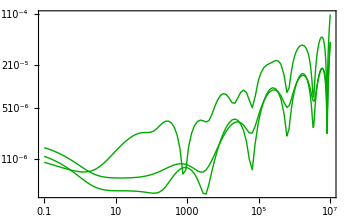

```mathematica
ErroRVFf=ListLogLogPlot[Map[Transpose@{omega/(2 Pi),difRVFAm2[[All,#]]}&,Range[nc]],PlotStyle->Darker[Green]]
```

# Ajuste de Matrizes Idempotentes (usando polos do ajuste de H modal)

```mathematica
ppolos=polosRVFAm2;
AbsoluteTiming[Do[pp=RVFpolos[ppolos,omega,Am2Tr,TemD,TemE];ppolos=pp,{niter}]];
polosRVFHmodal=ppolos;
```

```mathematica
M2=Table[0,{nc}];
```

```mathematica
AbsoluteTiming[Do[{ω=sk[[nm]],
M1[[nm]]=Table[Transpose@{evelho[[All,i]]}.{Inverse[evelho][[i,All]]} Am2[[nm,i]],{i,3}] ; (*corregido*)
},{nm,1,nf}]]
```

{0.03125,Null}

```mathematica
nM2=nc*(nc+1)/2;
Table[M2[[nm]]=descompmatrlarga[M1[[All,nm]]]//Chop,{nm,3}];
```

```mathematica
residuosRVFHmodal=TermDRVFM2=TermERVFM2=Table[0,{nc},{nM2}];Table[Do[{residuosRVFHmodal[[i,nm]],TermDRVFM2[[i,nm]],TermERVFM2[[i,nm]]}=res[polosRVFHmodal,omega,M2[[i,All,nm]],TemD,TemE],{nm,nM2}],{i,nc}];
```

```mathematica
funcoesRVFM2=difRMSRVFM2=PontosRVFElemM2=difRVFM2=Table[0,{nc}];
Table[{funcoesRVFM2[[i]],PontosRVFElemM2[[i]],difRMSRVFM2[[i]],difRVFM2[[i]]}=calcelem[polosRVFHmodal,residuosRVFHmodal[[i]],omega,M2[[i]],TermDRVFM2[[i]],TermERVFM2[[i]],nM2],{i,nc}];
```

## Ajuste del Valor Absoluto de Elementos das Matrizes Idempotentes

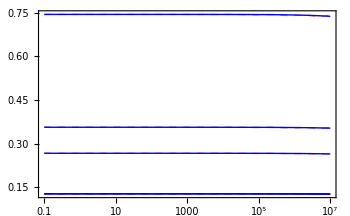
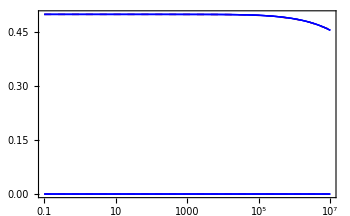
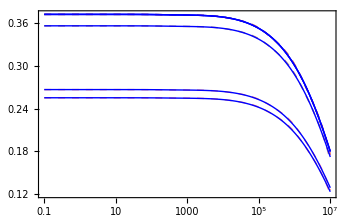

```mathematica
GrelemRVF=Table[ListLogLinearPlot[Map[Transpose@{omega/(2 Pi),Abs[PontosRVFElemM2[[j,All,#]]]}&,Range[nM2]],PlotStyle->Table[{Thick,RGBColor[i/nc,0.5,0.5],Dashed},{i,nM2}]],{j,1,nc}];
GrElemfun=Table[ListLogLinearPlot[Map[Transpose@{omega/(2 Pi),Abs[M2[[j,All,#]]]}&,Range[nM2]],PlotStyle->Blue],{j,1,nc}];
Show[GrelemRVF[[#]],GrElemfun[[#]]]&/@Range[nc]
```

## Ajuste del Argumento de Elementos das Matrizes Idempotentes

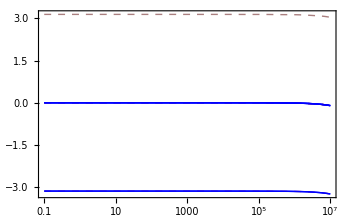
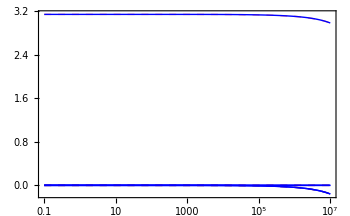
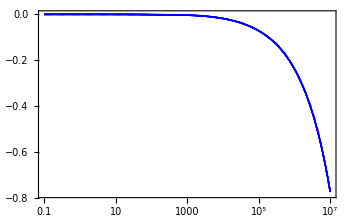

```mathematica
GrelemRVF=Table[ListLogLinearPlot[Map[Transpose@{omega/(2 Pi),UnwrapPhase[Arg[PontosRVFElemM2[[j,All,#]]]]}&,Range[nM2]],PlotStyle->Table[{Thick,RGBColor[i/nc,0.5,0.5],Dashed},{i,nM2}]],{j,1,nc}];
GrElemfun=Table[ListLogLinearPlot[Map[Transpose@{omega/(2 Pi),UnwrapPhase[Arg[M2[[j,All,#]]]]}&,Range[nM2]],PlotStyle->Blue],{j,1,nc}];
Show[GrelemRVF[[#]],GrElemfun[[#]]]&/@Range[nc]
```

## Error del Ajuste das Matrizes Idempotentes

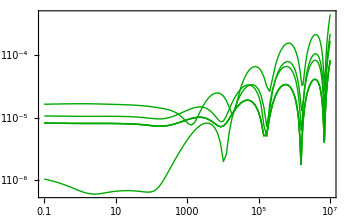
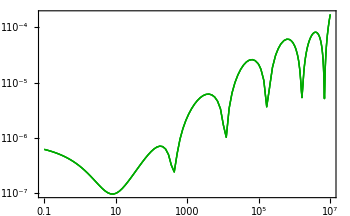
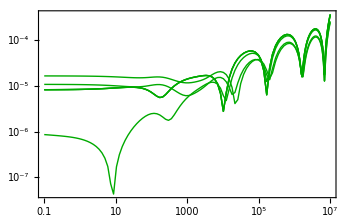

```mathematica
ErroRVFf=Table[ListLogLogPlot[Map[Transpose@{omega/(2 Pi),difRVFM2[[j,All,#]]}&,Range[nM2]],PlotStyle->Darker[Green]],{j,1,nc}];
Show[ErroRVFf[[#]]]&/@Range[nc]
```

```mathematica
(*TableForm[polosRVFHmodal]
TableForm[residuosRVFHmodal]*)
```